# Method of Steepest Descent

### Author

Eric W. Weisstein
April 27, 2008

This notebook downloaded from http://mathworld.wolfram.com/notebooks/Optimization/MethodofSteepestDescent.nb.

For more information, see Eric's MathWorld entry http://mathworld.wolfram.com/MethodofSteepestDescent.html.

©2008 Wolfram Research, Inc. except for portions noted otherwise

## Function

```mathematica
f[x_]:=x^3-2x^2+2
```

```mathematica
Solve[f'[y]==0,y]
```

{{y→0},{y→4/3}}

## Code

```mathematica
SteepestDescent[f_,x0_:0,n_:20,eps_:.1]:=Module[{x=NestList[#-eps f'[#]&,x0,n]},
Transpose[{x,f/@x}]
]
```

## Figure

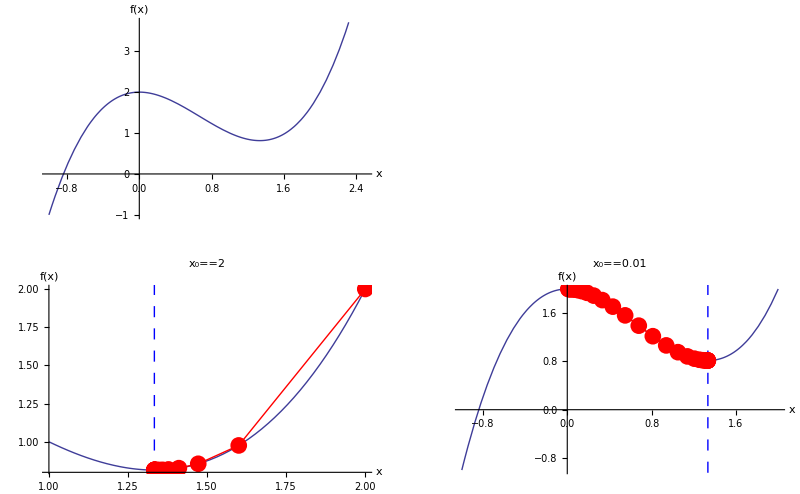

```mathematica
Show[GraphicsArray[
{
{Plot[f[x],{x,-1,2.5},
AxesLabel->{HoldForm[x],HoldForm[f[x]]}]},
Plot[f[x],{x,#[[1,1]],#[[1,2]]},Epilog->{Red,PointSize[.03],Point/@#[[2]],Line[#[[2]]],
Blue,Dashing[{.02}],Line[{{4/3,-10},{4/3,10}}]},
AxesLabel->{HoldForm[x],HoldForm[f[x]]},
PlotLabel->HoldForm[Subscript[x, 0]]==#[[3]],
PlotRange->All]&/@{
{{1,2},SteepestDescent[f,2,20,.1],2},
{{-1,2},SteepestDescent[f,.01,30,.1],.01}
}
}
]]
```

```mathematica
f[{x1_,x2_}]:=x1^2+x2^2
fp[{x1_,x2_}]:={2x1,2x2}
```

```mathematica
D[Sin[1/2 x1^2-1/4 x2^2+3]Cos[2x1+1-Exp[x2]],x2]
```

-1/2 x2 Cos[1-ⅇ^x2+2 x1] Cos[3+x1^2/2-x2^2/4]+ⅇ^x2 Sin[1-ⅇ^x2+2 x1] Sin[3+x1^2/2-x2^2/4]

```mathematica
f[{x1_,x2_}]:=Sin[1/2 x1^2-1/4 x2^2+3]Cos[2x1+1-Exp[x2]]
fp[{x1_,x2_}]:=-
{x1 Cos[1-ⅇ^x2+2 x1] Cos[3+x1^2/2-x2^2/4]-2 Sin[1-ⅇ^x2+2 x1] Sin[3+x1^2/2-x2^2/4],
-1/2 x2 Cos[1-ⅇ^x2+2 x1] Cos[3+x1^2/2-x2^2/4]+ⅇ^x2 Sin[1-ⅇ^x2+2 x1] Sin[3+x1^2/2-x2^2/4]}
```

```mathematica
SteepestDescent[f_,x10_:-0.5,x20_:0.5,n_:20,eps_:.1]:=Module[{x=NestList[#-eps fp[#]&,{x10,x20},n]},
Transpose[{x,f/@x}]
]
```

```mathematica
SteepestDescent[f,0.5,0.5,5,.25]
```

{{{0.5,0.5},0.5},{{0.25,0.25},0.125},{{0.125,0.125},0.03125},{{0.0625,0.0625},0.0078125},{{0.03125,0.03125},0.00195313},{{0.015625,0.015625},0.000488281}}

```mathematica
SteepestDescentXY[f_,x10_:-0.5,x20_:0.5,n_:20,eps_:.1]:=Module[{x=NestList[#-eps fp[#]&,{x10,x20},n]},
x
]
```

```mathematica
SteepestDescentXY[f,0.5,0.5,5,.25]
```

{{0.5,0.5},{0.25,0.25},{0.125,0.125},{0.0625,0.0625},{0.03125,0.03125},{0.015625,0.015625}}

```mathematica
SteepestDescentXY[f,0.5,0.5,3,.25]
```

{{0.5,0.5},{0.25,0.25},{0.125,0.125},{0.0625,0.0625}}

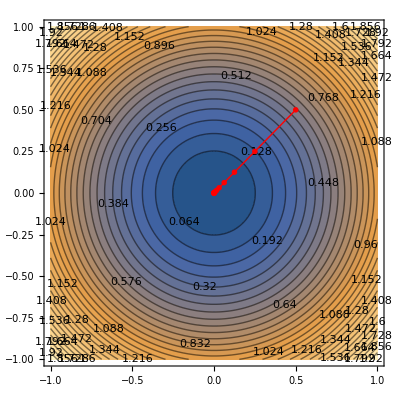

```mathematica
ContourPlot[
f[{x1,x2}],{x1,-1,1},{x2,-1,1},Contours->30,PlotPoints->30,ContourLabels->All,
Epilog->{Red,PointSize[.01],Point[#],Line[#]},
PlotRange->All]&[SteepestDescentXY[f,0.5,0.5,15,.25]]
```

```mathematica
Plot3D[f[{x1,x2}],{x1,-1,1},{x2,-1,1}]
```

-Graphics3D-

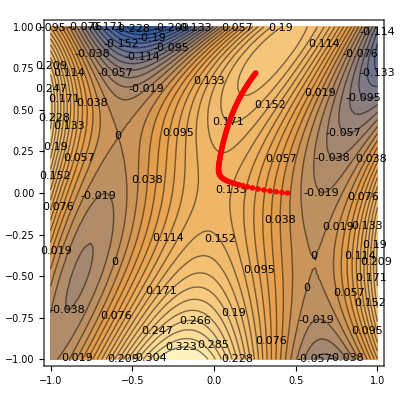

```mathematica
ContourPlot[
f[{x1,x2}],{x1,-1,1},{x2,-1,1},Contours->30,PlotPoints->30,ContourLabels->All,
Epilog->{Red,PointSize[.01],Point[#],Line[#]},
PlotRange->All]&[SteepestDescentXY[f,0.45,0.,100,.1]]
```